```mathematica
(* Definition Y: single pixel intensity, S: mask, X: target image*)
Y = S.X;
(* Goal find S such that Sᵀ Y = X*)
Sᵀ .Y == X;
```

```mathematica
(* Moore Penrose Pseudoinverse *)
(* S is row semi-orthogonal (m < n), i.e. S.Sᵀ == I *)
Clear[S]
Y == S.X;
Y == S.(Sᵀ.Inverse[Sᵀ]).X;
Y == (S.Sᵀ).Inverse[Sᵀ].X;
Sᵀ.Inverse[S.Sᵀ].Y==X;
```

```mathematica
(* Test using 8 rows of hadamard matrix *)
n=2^2;
H = HadamardMatrix[n];
S= Table[Flatten@Outer[Times,H[[;;,i]], H[[j,;;]]],{i, n},{j,n}]//Flatten[#,1]&;
S =S[[1;;8]]; (* Take only 8 rows *)
Dimensions[S]
S.Sᵀ == IdentityMatrix[8]
(* In this case Inverse[S.Sᵀ] == I *)
```

{8,16}

True

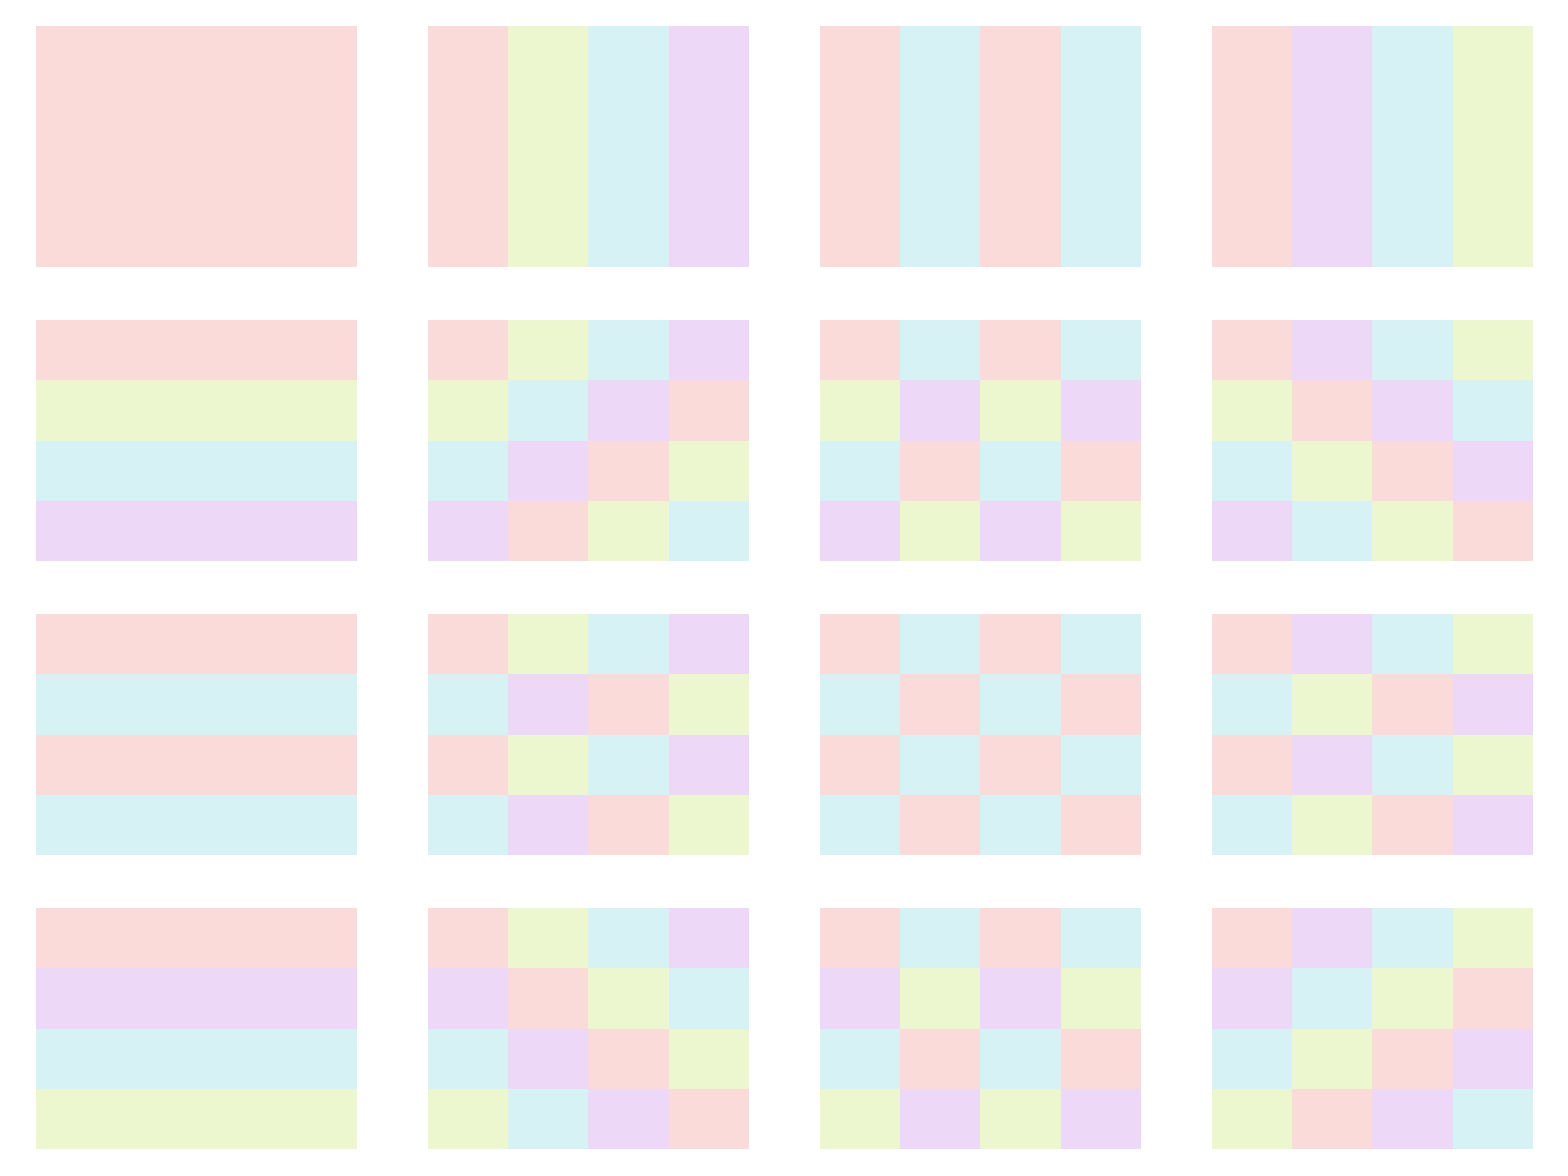
(-Graphics-)

(0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25 | 0.25
0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ
0.25 | -0.25 | 0.25 | -0.25 | 0.25 | -0.25 | 0.25 | -0.25 | 0.25 | -0.25 | 0.25 | -0.25 | 0.25 | -0.25 | 0.25 | -0.25
0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ
0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ
0.25+0. ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ
0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ
0.25 | 0.25 | 0.25 | 0.25 | -0.25 | -0.25 | -0.25 | -0.25 | 0.25 | 0.25 | 0.25 | 0.25 | -0.25 | -0.25 | -0.25 | -0.25
0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ
0.25 | -0.25 | 0.25 | -0.25 | -0.25 | 0.25 | -0.25 | 0.25 | 0.25 | -0.25 | 0.25 | -0.25 | -0.25 | 0.25 | -0.25 | 0.25
0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ
0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ
0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.25+0. ⅈ
0.25+0. ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ | 0.25+0. ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ
0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | -0.25+0. ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | 0.+0.25 ⅈ | 0.25+0. ⅈ | 0.-0.25 ⅈ | -0.25+0. ⅈ)

{8,16}

(1. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 1. | 0. | 0. | 0. | 0.
0. | 0. | 1. | 0. | 0. | 0. | 0. | 0.
0. | 1. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.
0. | 0. | 0. | 0. | 0. | 0. | 0. | 0.)

```mathematica
(* Test using 8 rows of hadamard matrix *)
n=2^2;
F[u_, v_]:= Fourier[SparseArray[{u, v}->1,{n, n}]];
Table[ComplexArrayPlot[F[i,j]], {i, n}, {j, n}]//MatrixForm
S= Table[Flatten@F[i, j],{i, n},{j,n}]//Flatten[#,1]&;
S//MatrixForm
S =S[[1;;8]]; (* Take only 8 rows *)
Dimensions[S]
Re@(S.Sᵀ) //MatrixForm
(* In this case Inverse[S.Sᵀ] == I *)
```